```mathematica
s=1;
vw=0.5;
m=100;
f0[w_]:=1/(Exp[w]+s);
df0[w_,k_]:=D[f0[w],{w,k}];
pwt[w_]=Sqrt[w^2-x^2];
pzt[w_]=gamw*(y*pwt-w*vw);
gamw = 1/Sqrt[1-vw^2];
```

```mathematica
-6/Pi^2*w*Sqrt[w^2-x^2]*df0[w,1]/.w->10/.x->0.1//N
```

0.0027601

```mathematica
g=x+(1-u)/u
```

```mathematica
D0[x_]:=If[x<100,NIntegrate[-6/Pi^2*w*Sqrt[w^2-x^2]*df0[w,1],{w,x,Infinity}],(6 x^2 BesselK[2,x])/π^2];
d0[x_]:=Exp[-x]*(2-12/Pi^2+(c[[1]]*x^c[[10]]+c[[9]]*x^c[[11]])/(c[[2]]*x^c[[3]]+c[[4]]*x^c[[5]]+c[[6]]*x^c[[7]]+c[[8]]))+6*x^2/Pi^2*BesselK[2,x];
```

```mathematica
D0[1]
```

0.862783

```mathematica
s=-1;
d0bos[x_]:=Exp[-x]*(2-12/Pi^2-(0.812x^1.3894+0.1761x^2.5872)/(0.3138+1.141x^0.3323+2.731x^0.4637+0.3084x^2.5168))+6*x^2/Pi^2*BesselK[2,x];
```

```mathematica
s=1;
d0fer[x_]:=Exp[-x]*(1-12/Pi^2-(0.6174x^1.1654-0.1681x^2.528)/(1.4805+2.2303x^0.6479-1.1634x^1.9991+1.0523x^2.4888))+6*x^2/Pi^2*BesselK[2,x];
```

```mathematica
Q1[x_]:=If[x<100,NIntegrate[-3*x^2/(gamw*Pi^2*m^2)*Sqrt[w^2-x^2]*df0[w,2],{w,x,Infinity}],-3x^3/(gamw*Pi^2*m^2)*BesselK[1,x]];
q1fer[x_]:=-3*x^2/(2*gamw*Pi^2*m^2)*(-Exp[-x]+2*x*BesselK[1,x]);
q1bos[x_]:=-3*x/(2*gamw*Pi^2*m^2)*(Pi*Exp[-x]+2*x^2*BesselK[1,x]);
```

```mathematica
coeff=Import["/home/johann/Documents/Projects/hobby/Function_optimization/D0_test.dat","Table",HeaderLines->1];
smallOnes = TakeSmallest[coeff[[All,Length[coeff[[1]]]]],4];
minEps={};
Do[AppendTo[minEps,Position[coeff,smallOnes[[i]]]],{i,Length[smallOnes]}]
```

```mathematica
i=1;
c=coeff[[minEps[[i,1,1]],;;Length[coeff[[1]]]-1]]
coeff[[minEps[[i,1,1]]]]
```

{-1.05498,-1.7041,0.746699,1.59789,2.59575,1.50629,1.80536,1.46708,-0.760034,2.61513,2.21302}

{-1.05498,-1.7041,0.746699,1.59789,2.59575,1.50629,1.80536,1.46708,-0.760034,2.61513,2.21302,0.0000934197}

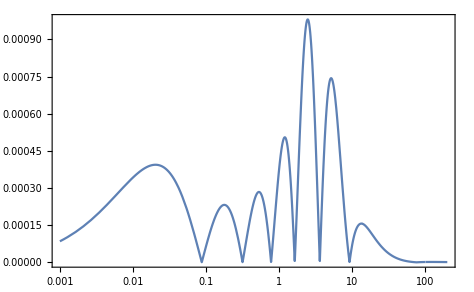

```mathematica
LogLinearPlot[{Abs[d0fer[x]/D0[x]-1]},{x,10^-3,200},PlotTheme->"FrameGrid",PlotRange->All]
```

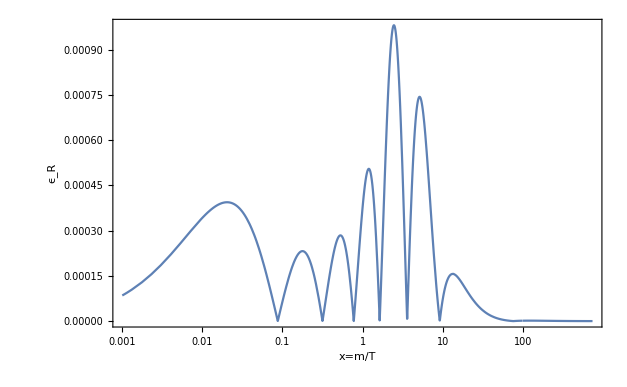

```mathematica
LogLinearPlot[{Abs[d0fer[x]/D0[x]-1]},{x,10^-3,1000},PlotTheme->"FrameGrid",PlotRange->All,FrameLabel->{Style["x=m/T",18],Style["ϵ_R",18]}]
```

```mathematica
c0=1.984;
b2appr[x_]:=Exp[-x]*(1+2.627/x+2/x^2)/(0.033*x^(c0/5)-0.102*x^(c0/4)+0.113*x^(c0/3)+1.162*x^(c0/2)+(2x/Pi)^c0+1)^(1/(2c0));
```

```mathematica
b2inf[x_]:=1.2533141373155*Exp[-x]/Sqrt[x]*(1+1.875/x*(1+0.4375/x*(1-0.375/x*(1-1.03125/x*(1-1.625/x*(1-2.1875/x))))))
```

```mathematica
b2good[x_]:=If[x< 5, b2appr[x], b2inf[x]]
```

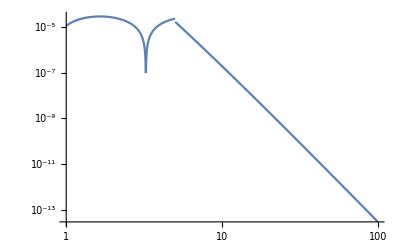

```mathematica
LogLogPlot[{Abs[b2good[x]/(BesselK[2,x])-1]},{x,1,10^2},PlotRange->Full]
```

```mathematica
b1inf[x_]:=1.2533141373155*Exp[-x]/Sqrt[x]*(1+0.375/x*(1-0.31250/x*(1-0.875/x*(1-1.40625/x*(1-1.925/x*(1-2.4375/x))))));
```

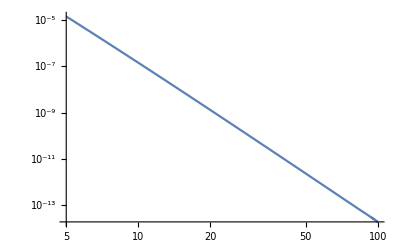

```mathematica
LogLogPlot[{Abs[b1inf[x]/(BesselK[1,x])-1]},{x,5,10^2},PlotRange->Full]
```

```mathematica
(s-(m1+m2)^2)*(s-(m1-m2)^2)//Expand//FullSimplify
```

m1^4+(m2^2-s)^2-2 m1^2 (m2^2+s)

```mathematica
0.2222222222222222222222222222222*3
```

0.666666666666666666666666666667